```mathematica
Quit[]
```

```mathematica
C1=1;C2=2;C3=3;C4=4;C5=5;C6=6;R1=1;R2=1;
A=({{1/R1+s*C1+s*C5, -s*C5, -s*C1, 0}, {-s*C5, s*C5+s*C2+1/R2, 0, -s*C2}, {-s*C1, 0, s*C1+s*C3+s*C6, -s*C6}, {0, -s*C2, -s*C6, s*C6+s*C4+s*C2}})
```

{{1+6 s,-5 s,-s,0},{-5 s,1+7 s,0,-2 s},{-s,0,10 s,-6 s},{0,-2 s,-6 s,12 s}}

```mathematica
B=({{E1/R1}, {0}, {0}, {0}})
```

{{E1},{0},{0},{0}}

```mathematica
LinearSolve[A,B]
```

{{(E1 (21+137 s))/(21+260 s+247 s^2)},{(108 E1 s)/(21+260 s+247 s^2)},{(E1 (3+35 s))/(21+260 s+247 s^2)},{(E1 (3+71 s))/(2 (21+260 s+247 s^2))}}

0.00202005 (238.227 2.71828^(-0.96448 t)-21.7734 2.71828^(-0.0881514 t))

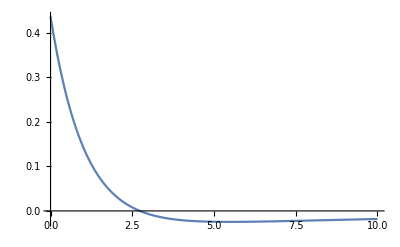

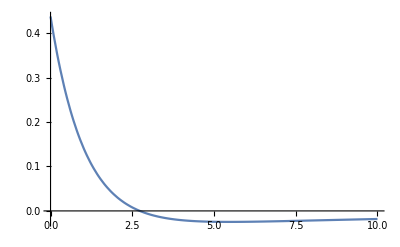

```mathematica
sal1[t_]=InverseLaplaceTransform[(108 s)/(21+260 s+247 s^2),s,t]//N
Plot[sal1[t],{t,0,10},PlotRange->All]
Plot[0.4813*Exp[-0.9645*t]-0.0440*Exp[-0.0882*t],{t,0,10},PlotRange->All]
```

```mathematica
Quit[]
```

```mathematica
C1=0.1;C2=0.1;C3=0.1;C4=0.1;C5=0.1;R1=1;R2=1;R3=1;R4=1;R5=1;
```

```mathematica
A=({{1/R1+s*C1+1/R2, -1/R2, 0, 0, 0}, {-1/R1, 1/R2+s*C2+1/R3, -1/R3, 0, 0}, {0, -1/R3, 1/R3+s*C3+1/R4, -1/R4, 0}, {0, 0, -1/R4, 1/R4+s*C4+1/R5, -1/R5}, {0, 0, 0, -1/R5, 1/R5+s*C5}})
```

{{2+0.1 s,-1,0,0,0},{-1,2+0.1 s,-1,0,0},{0,-1,2+0.1 s,-1,0},{0,0,-1,2+0.1 s,-1},{0,0,0,-1,1+0.1 s}}

```mathematica
B=({{E1/R1}, {0}, {0}, {0}, {0}})
```

{{E1},{0},{0},{0},{0}}

```mathematica
tensiones=LinearSolve[A,B]
```

{{(10. E1 (10000.+10000. s+1500. s^2+70. s^3+1. s^4))/(100000.+150000. s+35000. s^2+2800. s^3+90. s^4+1. s^5)},{(100. E1 (1000.+600. s+50. s^2+1. s^3))/(100000.+150000. s+35000. s^2+2800. s^3+90. s^4+1. s^5)},{(1000. E1 (100.+30. s+1. s^2))/(100000.+150000. s+35000. s^2+2800. s^3+90. s^4+1. s^5)},{(10000. E1 (10.+1. s))/(100000.+150000. s+35000. s^2+2800. s^3+90. s^4+1. s^5)},{(100000. E1)/(100000.+150000. s+35000. s^2+2800. s^3+90. s^4+1. s^5)}}

```mathematica
salida=ReplaceAll[Extract[tensiones,{5,1}]/1,E1->1]
```

100000./(100000.+150000. s+35000. s^2+2800. s^3+90. s^4+1. s^5)

```mathematica
tempo[t_]=Simplify[InverseLaplaceTransform[salida,s,t]]
```

0.553877 ⅇ^(-36.8251 t)-1.78831 ⅇ^(-28.3083 t)+2.72021 ⅇ^(-17.1537 t)-2.49983 ⅇ^(-6.90279 t)+1.01405 ⅇ^(-0.810141 t)

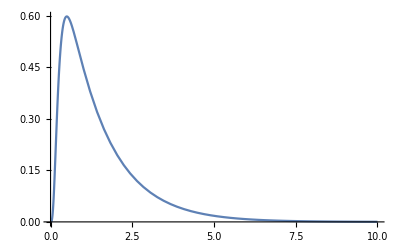

```mathematica
Plot[tempo[t],{t,0,10}, PlotRange->All]
```